# Metric tensor using GRQUICK

## Interpolation of the metric tensor

Let' s interpolate them metric tensor components to get analytical prescription and save it to file for faster calculations.

```mathematica
gridStep=0.01;
λr={-1,1};
χr={0,1.5};
```

```mathematica
gTab=Flatten[Table[{λ,χ,gC[λ,χ]},{λ,λr⟦1⟧,λr⟦2⟧,gridStep},{χ,χr⟦1⟧,χr⟦2⟧,gridStep}],1];
```

```mathematica
Export[NotebookDirectory[]<>"gTab_n=5_gridStep=0,01.m",gTab];
```

```mathematica
gTab=Import[NotebookDirectory[]<>"gTab_n=5_gridStep=0,01.m"];
```

```mathematica
gTablen=Dimensions[gTab]⟦1⟧;
λS=gTab[[#]]⟦1⟧&/@Range[1,gTablen];
χS=gTab⟦#⟧⟦2⟧&/@Range[1,gTablen];
gS=gTab⟦#⟧⟦3⟧&/@Range[1,gTablen];
gS11=gTab⟦#⟧⟦3⟧⟦1,1⟧&/@Range[1,gTablen];
gS12=gTab⟦#⟧⟦3⟧⟦1,2⟧&/@Range[1,gTablen];
gS22=gTab⟦#⟧⟦3⟧⟦2,2⟧&/@Range[1,gTablen];
```

-Graphics-

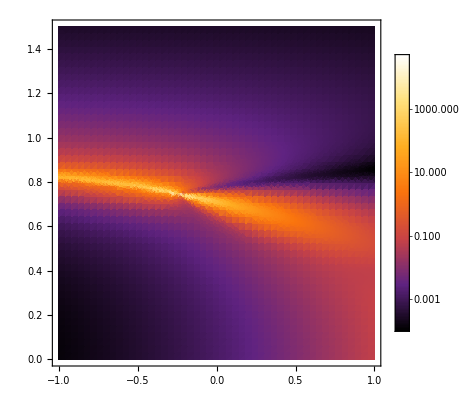

```mathematica
ListDensityPlot[Transpose@{λS,χS,Map[Det,gS]},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"]
DensityPlot[Det[gC[λ,χ]],Flatten@{λ,λr},Flatten@{χ,χr},Evaluate@densityPlotOptions,PlotPoints->50,ScalingFunctions->"Log10"]
```

```mathematica
interpolationMethod={InterpolationOrder->1,Method->"Spline"};
gI11=Interpolation[Transpose@{λS,χS,gS11},Evaluate@interpolationMethod];
gI12=Interpolation[Transpose@{λS,χS,gS12},Evaluate@interpolationMethod];
gI22=Interpolation[Transpose@{λS,χS,gS22},Evaluate@interpolationMethod];
gI[λ_,χ_]={{gI11[λ,χ],gI12[λ,χ]},{gI12[λ,χ],gI22[λ,χ]}};
```

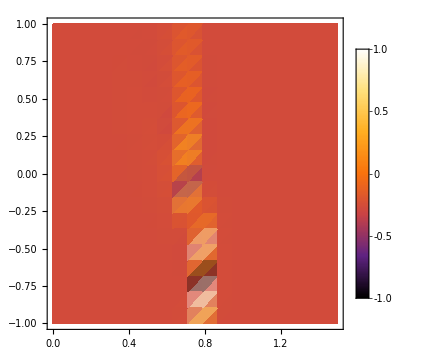
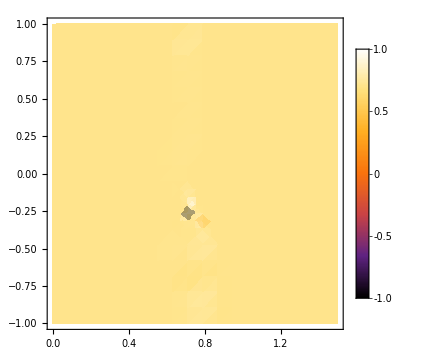
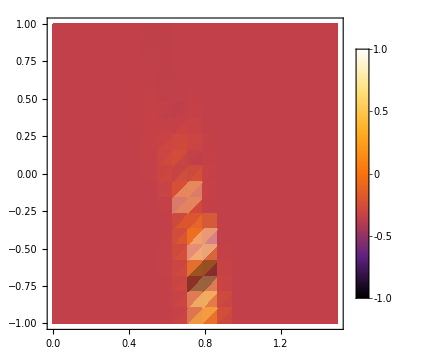

```mathematica
densitycheck={FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",ImageSize->Medium,PlotPoints->20,PlotRange->{Automatic,Automatic,{-1,1}},PlotLegends->BarLegend[{Automatic,{-1,1}}]};
Quiet@{DensityPlot[1-(gC[λ,χ]⟦1,1⟧)/gI11[λ,χ],0Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck],
DensityPlot[1-(gC[λ,χ]⟦1,2⟧)/gI12[λ,χ],Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck],
DensityPlot[1-(gC[λ,χ]⟦2,2⟧)/gI22[λ,χ],Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck]}
```

## GRQUICK

```mathematica
Metin[gI[λ,χ],{λ,χ}]
```

Metric Success

```mathematica
DensityPlot[ArcTan@Christoffel[{{0},{0,1}}],{λ,-0.2,0.4},{χ,0,1},Evaluate@densityPlotOptions,PlotPoints->30]
```

General::ivar: 0. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

Geodesics finds the form for right side of the geodesic equation and geo⟦1⟧, geo⟦2⟧ as two interpolation type functions for λ[τ], χ[τ] and the boundary/initial value problem needs to be solved for geo⟦1⟧ = 0, geo⟦2⟧ = 0.

```mathematica
Einstein[0,0];
Setlight[1];
geo=Geodesics[τ];
eqn={geo⟦1⟧==0,geo⟦2⟧==0}/.{λ->λp,χ->χp};
```

```mathematica
denp=ListDensityPlot[Transpose@{λS,χS,Map[Det,gS]},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"];
(*denp=DensityPlot[Det[gI[λ,χ]],{λ,-0.5,1},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"];*)
```

### Boundary value problem

```mathematica
tmax=10;
dirichletE[i1_,i2_,f1_,f2_]:={λp[0]==i1,χp[0]==i2,λp[tmax]==f1,χp[tmax]==f2};
```

```mathematica
solE=NDSolve[Join[eqn,dirichletE[0,0,0.3,0.6]],{λp,χp},{τ,0,tmax},Method->"Shooting",AccuracyGoal->4,PrecisionGoal->4]
```

{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}}

```mathematica
solM=Quiet@NDSolve[Join[eqn,dirichlet[0,0,0.3,#]],{λp,χp},{τ,0,τmax},Method->"Shooting",AccuracyGoal->3,PrecisionGoal->3]&/@Range[0.1,0.5,0.2]
```

{{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}}}

```mathematica
(*sol=NDSolve[Join[eqn,dirichlet],{λp,χp},{τ,0,1},Method->{"Shooting","StartingInitialConditions"->{χp[0]==init[[1]],λp[0]==init[[2]],χp'[0]==1,λp'[0]==1}}]*)
```

```mathematica
parpB=ParametricPlot[{λp[τ],χp[τ]}/.solE,{τ,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{denp,parpB}]
```

-Graphics-

### Initial value problem

```mathematica
cauchyE[l1_,l2_,x1_,x2_]:={λp[0]==l1,χp[0]==x1,λp'[0]==l2,χp'[0]==x2,
WhenEvent[χp[τ]<-0.1||χp[τ]>1||λp[τ]<-0.6||λp[τ]>1,"StopIntegration"]};
```

```mathematica
solME=Quiet@ParallelTable[NDSolve[Join[eqn,cauchyE[0,Cos[θ],0,Sin[θ]]],{λp,χp},{τ,0,τmax}],{θ,0,π,π/20}]
```

{{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[{{0., 10.}}, <>],χp→InterpolatingFunction[{{0., 10.}}, <>]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}}}

```mathematica
parp=ParametricPlot[{λp[τ],χp[τ]}/.solME,{τ,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{denp,parp}]
```

-Graphics-